```mathematica
ListaC={{0,90},
{1,156},
{2, 197},
{3, 253},
{4, 255},
{5, 307},
{6, 267},
{7, 256},
{8, 259},
{9, 260},
{10,242},
{11,261},
{12, 298},
{13, 293},
{14, 325},
{15, 354},
{16, 351},
{17, 363},
{18, 387},
{19, 348},
{20, 309},
{21, 334},
{22 ,289},
{23, 267},
{24, 259},
{25, 256},
{26 ,211},
{27 ,219},
{28 ,193},
{29 ,199},
{30 ,183},
{31 ,207},
{32 ,182},
{33 ,197},
{34 ,221},
{35 ,195},
{36 ,194},
{37 ,197},
{38 ,199},
{39 ,211},
{40 ,200},
{41 ,212},
{42 ,230},
{43 ,239},
{44 ,228},
{45 ,219},
{46 ,244},
{47 ,260},
{48 ,227},
{49 ,243},
{50 ,230},
{51 ,214},
{52 ,231},
{53 ,216},
{54 ,246},
{55 ,231},
{56 ,252},
{57 ,292},
{58 ,249},
{59 ,242},
{60 ,243},
{61 ,222},
{62 ,275},
{63 ,267},
{64 ,264},
{65 ,252},
{66 ,280},
{67 ,273},
{68 ,268},
{69 ,275},
{70 ,272},
{71 ,290},
{72 ,237},
{73 ,277},
{74 ,309},
{75 ,284},
{76 ,270},
{77 ,276},
{78 ,255},
{79 ,236},
{80 ,251},
{81 ,232},
{82 ,225},
{83 ,209},
{84 ,170},
{85 ,179},
{86 ,168},
{87 ,142},
{88 ,111},
{89 ,102},
{90 ,74},
{91 ,73},
{92 ,58},
{93 ,63},
{94 ,39},
{95 ,32},
{96 ,16},
{97 ,12},
{98 ,12},
{99 ,6},
{100 ,6},
{101 ,4},
{102 ,4},
{103 ,1}}
```

{{0,90},{1,156},{2,197},{3,253},{4,255},{5,307},{6,267},{7,256},{8,259},{9,260},{10,242},{11,261},{12,298},{13,293},{14,325},{15,354},{16,351},{17,363},{18,387},{19,348},{20,309},{21,334},{22,289},{23,267},{24,259},{25,256},{26,211},{27,219},{28,193},{29,199},{30,183},{31,207},{32,182},{33,197},{34,221},{35,195},{36,194},{37,197},{38,199},{39,211},{40,200},{41,212},{42,230},{43,239},{44,228},{45,219},{46,244},{47,260},{48,227},{49,243},{50,230},{51,214},{52,231},{53,216},{54,246},{55,231},{56,252},{57,292},{58,249},{59,242},{60,243},{61,222},{62,275},{63,267},{64,264},{65,252},{66,280},{67,273},{68,268},{69,275},{70,272},{71,290},{72,237},{73,277},{74,309},{75,284},{76,270},{77,276},{78,255},{79,236},{80,251},{81,232},{82,225},{83,209},{84,170},{85,179},{86,168},{87,142},{88,111},{89,102},{90,74},{91,73},{92,58},{93,63},{94,39},{95,32},{96,16},{97,12},{98,12},{99,6},{100,6},{101,4},{102,4},{103,1}}

```mathematica
L=Length[ListaC]
```

104

```mathematica
∑_(j=1)^L ListaC[[j]][[2]]
```

22263

```mathematica
μ=N[∑_(j=1)^L ((ListaC[[j]][[1]]*ListaC[[j]][[2]])/22263)]
```

44.056

```mathematica
σ=N[√(∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^2*ListaC[[j]][[2]])/22263))]
```

26.1825

```mathematica
Length[ListaC]
```

104

```mathematica
Lista2=Table[{ListaC[[j]][[1]],(ListaC[[j]][[2]])/22263},{j,1,Length[ListaC]}];
```

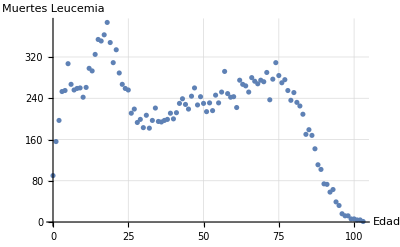

```mathematica
g1=ListPlot[ListaC ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Leucemia"}]
```

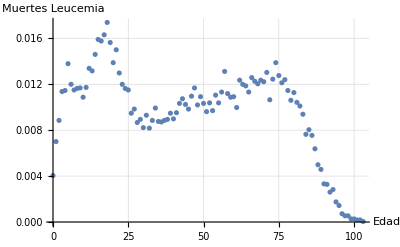

```mathematica
g3=ListPlot[Lista2 ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Leucemia"}]
```

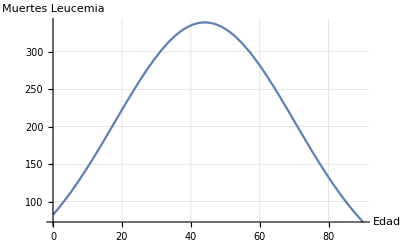

```mathematica
g2=Plot[22263*1/(√(2π)σ) ⅇ^(-(x-μ)^2/(2 σ^2)),{x,0,90},GridLines->Automatic,AxesLabel->{"Edad","Muertes Leucemia"}]
```

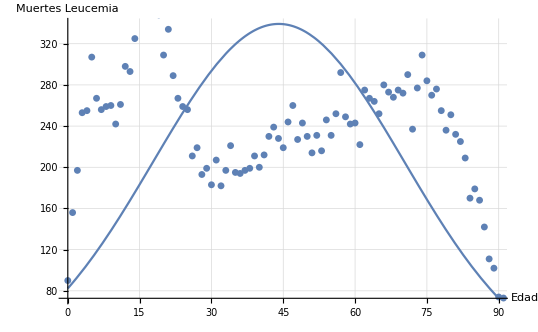

```mathematica
Show[g2,g1]
```